```mathematica
Clear[h,Δ,kx,ky,H,Δuu,Δud,Δdu,Δdd]
ξ[kx_,ky_]=(1-tx Cos[kx]-ty Cos[ky]);
h[kx_,ky_]=ξ[kx,ky]*PauliMatrix[0]+
{bx,by,bz}.Table[PauliMatrix[i],{i,3}];
h2[kx_,ky_]=-PauliMatrix[3].h[kx,ky]*.PauliMatrix[3];


Δuu[kx_,ky_]=+(dx Sin[kx]-ⅈ dy Sin[ky]);
Δdd[kx_,ky_]=+(dx Sin[kx]+ⅈ dy Sin[ky]);
Δud[kx_,ky_]=-(sx*Cos[kx]+sy*Cos[ky]);
Δdu[kx_,ky_]=+(sx*Cos[kx]+sy*Cos[ky]);
Δ[kx_,ky_]={{Δuu[kx,ky],-Δud[kx,ky]},{Δdu[kx,ky],-Δdd[kx,ky]}};

Hpr[kx_,ky_]=ArrayFlatten[{{h[kx,ky],Δ[kx,ky]},{Δ[kx,ky]*,h2[kx,ky]}}];

H[kx_,ky_]=Refine[Hpr[kx,ky],{bx∈Reals,by∈Reals,bz∈Reals,sx∈Reals,sy∈Reals,kx∈Reals,ky∈Reals&&dx∈Reals&&dy∈Reals&&tx∈Reals&&ty∈Reals}]
%//MatrixForm
```

{{1+bz-tx Cos[kx]-ty Cos[ky],bx-ⅈ by,dx Sin[kx]-ⅈ dy Sin[ky],sx Cos[kx]+sy Cos[ky]},{bx+ⅈ by,1-bz-tx Cos[kx]-ty Cos[ky],sx Cos[kx]+sy Cos[ky],-dx Sin[kx]-ⅈ dy Sin[ky]},{dx Sin[kx]+ⅈ dy Sin[ky],sx Cos[kx]+sy Cos[ky],-1-bz+tx Cos[kx]+ty Cos[ky],bx+ⅈ by},{sx Cos[kx]+sy Cos[ky],-dx Sin[kx]+ⅈ dy Sin[ky],bx-ⅈ by,-1+bz+tx Cos[kx]+ty Cos[ky]}}

(1+bz-tx Cos[kx]-ty Cos[ky] | bx-ⅈ by | dx Sin[kx]-ⅈ dy Sin[ky] | sx Cos[kx]+sy Cos[ky]
bx+ⅈ by | 1-bz-tx Cos[kx]-ty Cos[ky] | sx Cos[kx]+sy Cos[ky] | -dx Sin[kx]-ⅈ dy Sin[ky]
dx Sin[kx]+ⅈ dy Sin[ky] | sx Cos[kx]+sy Cos[ky] | -1-bz+tx Cos[kx]+ty Cos[ky] | bx+ⅈ by
sx Cos[kx]+sy Cos[ky] | -dx Sin[kx]+ⅈ dy Sin[ky] | bx-ⅈ by | -1+bz+tx Cos[kx]+ty Cos[ky])

```mathematica
H[kx,ky]/.{bx->0,by->0,bz->0,sx->0,sy->0}//FullSimplify
```

{{1-Cos[kx]-Cos[ky],0,Sin[kx]-ⅈ Sin[ky],0},{0,1-Cos[kx]-Cos[ky],0,-Sin[kx]-ⅈ Sin[ky]},{Sin[kx]+ⅈ Sin[ky],0,-1+Cos[kx]+Cos[ky],0},{0,-Sin[kx]+ⅈ Sin[ky],0,-1+Cos[kx]+Cos[ky]}}

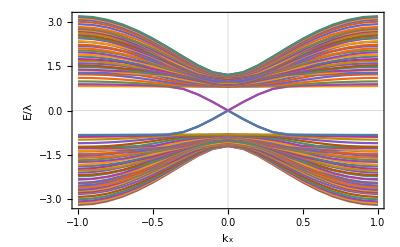

```mathematica
(* y-direction finite, periodic along x *)
Clear[δ,Hmixed,γ,λ,Δ];
γs=Range[-2,2,0.1];
((H[kx,ky]/.{bx->0.,by->0.2,bz->0,sx->0.,sy->0.1})*Exp[ⅈ*{0,ky}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ ky y1-ⅈ ky y2)->δ[y1,y2],ⅇ^(-ⅈ kx+ⅈ ky y1-ⅈ ky y2) -> ⅇ^(-ⅈ kx)δ[y1,y2],ⅇ^(ⅈ ky+ⅈ ky y1-ⅈ ky y2)->δ[y1+1,y2],ⅇ^(-ⅈ ky+ⅈ ky y1-ⅈ ky y2)->δ[y1,y2+1],ⅇ^(ⅈ kx+ⅈ ky y1-ⅈ ky y2)->ⅇ^(ⅈ kx)δ[y1,y2]};
(* assign local real space Hamiltonian *)
Hmixed[y1_,y2_,kx_]=%;
δ[x_,y_]=If[x==y,1,0];
(* now construct the full one *)
Clear[Hfull];
pbc=False;
Hfull= ConstantArray[0,{Lx,Length[Hmixed[1,1,1,1]],Lx,Length[Hmixed[1,1,1,1]]}];
Do[
If[y2>0&&y2≤Ly,
Hfull[[y1,;;,y2,;;]]+=Hmixed[y1,y2,kx];
];

(* the boundary terms *)
If[y2==Ly+1&&pbc,
Hfull[[y1,;;,1,;;]]+=Hmixed[y1,y2,kx];
];
If[y2==0&&pbc,
Hfull[[y1,;;,Ly,;;]]+=Hmixed[y1,y2,kx];
];
,{y1,Ly},{y2,y1-1,y1+1}];
Hmat=ArrayReshape[Hfull,{Ly*4,Ly*4}];
ks = Table[N[(2π)/Lx n-π],{n,0,Lx}];
res = Table[orderedEigensystem[Hmat/.{kx->k,γ->0.,λ->1,Δ->0.}],{k,ks}];
ListPlot[res[[;;,1]]ᵀ,DataRange->MinMax[ks]/π,Joined->True,PlotTheme->"Scientific",FrameLabel->{"k_x","E/λ"}]
```

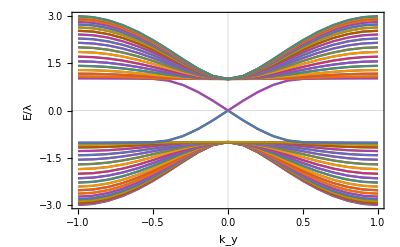

```mathematica
(* x-direction finite, periodic along y *)
Clear[δ,Hmixed,γ,λ,Δ];
γs=Range[-2,2,0.1];
((H[kx,ky]/.{bx->0,by->0,bz->0,sx->0,sy->0})*Exp[ⅈ*{kx,0}.({x1,y1}-{x2,y2})]//TrigToExp//ExpandAll)/.{ⅇ^(ⅈ kx x1-ⅈ kx x2)->δ[x1,x2],ⅇ^(-ⅈ kx+ⅈ kx x1-ⅈ kx x2) -> δ[x1,x2+1],ⅇ^(ⅈ ky+ⅈ kx x1-ⅈ kx x2)->δ[x1,x2] ⅇ^(ⅈ ky),ⅇ^(-ⅈ ky+ⅈ kx x1-ⅈ kx x2)->ⅇ^(-ⅈ ky)δ[x1,x2],ⅇ^(ⅈ kx+ⅈ kx x1-ⅈ kx x2)->δ[x1+1,x2]};
(* assign local real space Hamiltonian *)
Hmixed[x1_,x2_,ky_]=%;
δ[x_,y_]=If[x==y,1,0];
(* now construct the full one *)
Clear[Hfull];
pbc=False;
Hfull= ConstantArray[0,{Lx,Length[Hmixed[1,1,1]],Lx,Length[Hmixed[1,1,1]]}];
Do[
If[x1>0&&x1≤Lx,
Hfull[[x1,;;,x2,;;]]+=Hmixed[x1,x2,ky];
];

(* the boundary terms *)
If[x1==Lx+1&&pbc,
Hfull[[1,;;,x2,;;]]+=Hmixed[x1,x2,ky];
];

If[x1==0&&pbc,
Hfull[[Lx,;;,x2,;;]]+=Hmixed[x1,x2,ky];
];
,{x1,x2-2,x2+2},{x2,Lx}];
Hmat=ArrayReshape[Hfull,{Lx*4,Lx*4}];
ks = Table[N[(2π)/Ly n-π],{n,0,Ly}];
ListPlot[Table[Sort[Eigenvalues[Hmat/.{ky->k,γ->0.,λ->1,Δ->0.}]],{k,ks}]ᵀ,DataRange->MinMax[ks]/π,Joined->True,PlotTheme->"Scientific",FrameLabel->{"k_y","E/λ"}]
```

```mathematica
HPH = (H[kx,ky]/.{bz->0});
HPHFY =(HPH/.{Cos[kx]->0,Sin[kx]->0});
HPHFX =(HPH/.{Cos[ky]->0,Sin[ky]->0,bx->0,sx->0});
deq=(Normal[Series[HPHFX,{kx,0,1}]])//ExpandAll//FullSimplify;
deq//MatrixForm
```

(0 | -ⅈ by | kx | 0
ⅈ by | 0 | 0 | -kx
kx | 0 | 0 | ⅈ by
0 | -kx | -ⅈ by | 0)

```mathematica
HPHFX//MatrixForm
```

(1-Cos[kx] | -ⅈ by | Sin[kx] | 0
ⅈ by | 1-Cos[kx] | 0 | -Sin[kx]
Sin[kx] | 0 | -1+Cos[kx] | ⅈ by
0 | -Sin[kx] | -ⅈ by | -1+Cos[kx])

```mathematica
{eval,evec}=Eigensystem[deq]//FullSimplify;
sols=DeleteDuplicates[Flatten[Solve[{#==0},kx]&/@eval]]
({eval,evec}=Refine[Normal[Series[Eigensystem[deq/.{#}],{by,0,1}]],0<by<1&&0<bx<1&&0<sx<1])&/@{sols};
eval
evec
(*evec={evec[[1]],evec[[2]],{-ⅈ,0,0,1},{0,ⅈ,1,0}}*)
ps=Refine[{#}†.{#}&/@(evec)//FullSimplify,0<by<1&&0<bx<1&&0<sx<1];
Hproj=Refine[((#.(HPHFX).#//ExpandAll)//FullSimplify)&/@ps,0<by<1&&0<bx<1]//ExpandAll//FullSimplify;
MatrixForm/@Hproj
Eigensystem[Hproj[[1]]]
(Refine[Length[SingularValueList[#]],dy∈Reals&&ky∈Reals&&sy∈Reals&&0<by<1&&0<bx<1] )&/@Hproj
```

{kx→-by,kx→by}

{-2 by,2 by,0,0}

{{-ⅈ,-1,-ⅈ,1},{-ⅈ,1,ⅈ,1},{ⅈ,0,0,1},{0,ⅈ,1,0}}

{(4 (by+Sin[kx]) | -4 ⅈ (by+Sin[kx]) | 4 (by+Sin[kx]) | 4 ⅈ (by+Sin[kx])
4 ⅈ (by+Sin[kx]) | 4 (by+Sin[kx]) | 4 ⅈ (by+Sin[kx]) | -4 (by+Sin[kx])
4 (by+Sin[kx]) | -4 ⅈ (by+Sin[kx]) | 4 (by+Sin[kx]) | 4 ⅈ (by+Sin[kx])
-4 ⅈ (by+Sin[kx]) | -4 (by+Sin[kx]) | -4 ⅈ (by+Sin[kx]) | 4 (by+Sin[kx])),(-4 (by+Sin[kx]) | -4 ⅈ (by+Sin[kx]) | 4 (by+Sin[kx]) | -4 ⅈ (by+Sin[kx])
4 ⅈ (by+Sin[kx]) | -4 (by+Sin[kx]) | -4 ⅈ (by+Sin[kx]) | -4 (by+Sin[kx])
4 (by+Sin[kx]) | 4 ⅈ (by+Sin[kx]) | -4 (by+Sin[kx]) | 4 ⅈ (by+Sin[kx])
4 ⅈ (by+Sin[kx]) | -4 (by+Sin[kx]) | -4 ⅈ (by+Sin[kx]) | -4 (by+Sin[kx])),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

{{16 (by+Sin[kx]),0,0,0},{{ⅈ,-1,ⅈ,1},{-ⅈ,0,0,1},{-1,0,1,0},{ⅈ,1,0,0}}}

{1,1,4,4}

```mathematica
deq=(Normal[HPHF]//ExpandAll//FullSimplify)/.{Cos[ky]->0,Sin[ky]->0}//MatrixForm
```

(1-Cos[kx] | bx | Sin[kx] | 0
bx | 1-Cos[kx] | 0 | -Sin[kx]
Sin[kx] | 0 | -1+Cos[kx] | bx
0 | -Sin[kx] | bx | -1+Cos[kx])

```mathematica
deq=(Normal[HPHF]//ExpandAll//FullSimplify)/.{Cos[ky]->0,Sin[ky]->0}
```

{{1-Cos[kx],bx,Sin[kx],0},{bx,1-Cos[kx],0,-Sin[kx]},{Sin[kx],0,-1+Cos[kx],bx},{0,-Sin[kx],bx,-1+Cos[kx]}}

```mathematica
Hproj=Refine[((#.(deq).#//ExpandAll)//FullSimplify)&/@ps,0<by<1&&0<bx<1]//ExpandAll//FullSimplify;
MatrixForm/@Hproj
```

{(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

```mathematica
HPHF = (H[kx,ky]/.{bz->0,bx->0,by->0,sx->0,sy->0});
HPHF = (H[kx,ky]/.{bz->0,by->0,sx->0,sy->0});
(*HPH = (H[kx,ky]/.{bz->0,bx->0,sx->0,sy->0});*)
HPH = Normal[Series[HPHF,{ky,0,1}]];
deq=(Normal[HPH]//ExpandAll//FullSimplify)/.{Cos[kx]->0,Sin[kx]->0}
{eval,evec}=Eigensystem[deq]//FullSimplify;
sols=DeleteDuplicates[Flatten[Solve[{#==0},ky]&/@eval]]
sol=sols[[2]]
({eval,evec}=Refine[Normal[Series[Eigensystem[deq/.{#}],{by,0,1}]],0<by<1&&0<bx<1&&0<sx<1])&/@{sol};
eval
evec={evec[[1]],evec[[2]],{-ⅈ,0,0,1},{0,ⅈ,1,0}}
ps=Refine[{#}†.{#}&/@(evec)//FullSimplify,0<by<1&&0<bx<1&&0<sx<1];
Hproj=Refine[((#.(HPHF/.{sol}).#//ExpandAll)//FullSimplify)&/@ps,0<by<1&&0<bx<1]//ExpandAll//FullSimplify;
MatrixForm/@Hproj
(Refine[Length[SingularValueList[#]],dy∈Reals&&ky∈Reals&&sy∈Reals&&0<by<1&&0<bx<1] )&/@Hproj
```

{{0,bx,-ⅈ ky,0},{bx,0,0,-ⅈ ky},{ⅈ ky,0,0,bx},{0,ⅈ ky,bx,0}}

{ky→-bx,ky→bx}

ky→bx

{-2 bx,2 bx,0,0}

{{-ⅈ,ⅈ,-1,1},{-ⅈ,-ⅈ,1,1},{-ⅈ,0,0,1},{0,ⅈ,1,0}}

{(4 (-bx+Sin[bx]) | 4 (bx-Sin[bx]) | 4 ⅈ (bx-Sin[bx]) | -4 ⅈ (bx-Sin[bx])
4 (bx-Sin[bx]) | 4 (-bx+Sin[bx]) | -4 ⅈ (bx-Sin[bx]) | 4 ⅈ (bx-Sin[bx])
-4 ⅈ (bx-Sin[bx]) | 4 ⅈ (bx-Sin[bx]) | 4 (-bx+Sin[bx]) | 4 (bx-Sin[bx])
4 ⅈ (bx-Sin[bx]) | -4 ⅈ (bx-Sin[bx]) | 4 (bx-Sin[bx]) | 4 (-bx+Sin[bx])),(4 (bx-Sin[bx]) | 4 (bx-Sin[bx]) | 4 ⅈ (bx-Sin[bx]) | 4 ⅈ (bx-Sin[bx])
4 (bx-Sin[bx]) | 4 (bx-Sin[bx]) | 4 ⅈ (bx-Sin[bx]) | 4 ⅈ (bx-Sin[bx])
-4 ⅈ (bx-Sin[bx]) | -4 ⅈ (bx-Sin[bx]) | 4 (bx-Sin[bx]) | 4 (bx-Sin[bx])
-4 ⅈ (bx-Sin[bx]) | -4 ⅈ (bx-Sin[bx]) | 4 (bx-Sin[bx]) | 4 (bx-Sin[bx])),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

{1,1,4,4}